to do:

plot the parity operator Π=P_11+P_00-P_10-P_01. Apply a pi/2, iSWAP, pi/2, pi/2_n(θ,ϕ), see parity oscillation. See how it changes with detuning and XY8 pulse sequences.

Make the code run faster by precomputing the matrix exponentials for prior times.

# Two-qubit pulse sequences

## Gabriel Patenotte, 10/29/22

This code models a sequence of pulses applied to a two-qubit system. The pulses are given in pulseList, and relevant parameters such as the Rabi-frequency (Ω), detuning (δω_0), dipole-dipole coupling (J), simulation time (tMax), and spacing between pulses (τ_0) can be adjusted. Time evolution is computed by applying a set of unitary matrices to a wavefunction. This evolution method should work since the Hamiltonian is time-independent for the duration of each unitary operator.

To run the code press control/command+a followed by shift+enter.

The outputs consist of several plots. For a fixed τ0, I plot the evolution of various single and two-qubit states over time. I also show the Bloch sphere for each qubit. Lastly, I vary τ to see oscillation between gg and ee at t=tMax due to the dipolar interaction, like Lawrence does.

### Parameters

Ω = 100 π
δω_0 = 0
J = π
ψ(0) = (0 | 1 | 0 | 0)
τ0 = 41/160
t_Max = 4.19

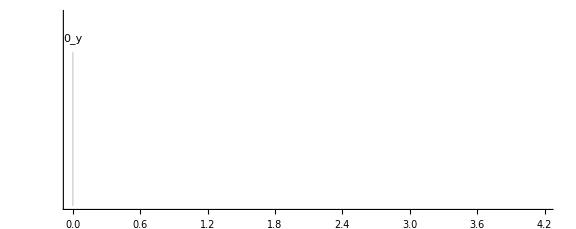

```mathematica
g={{1},{0}};e={{0},{1}};gg=KroneckerProduct[g,g];ge=KroneckerProduct[g,e];(*1-qubit and 2-qubit wavefunctions*)
Ω=100π;δω0=0;tRes=0.01;J=1π;τ0=(5-9/10)/16;ψ0=ge;
free={{0,"y",0}};
ramsey={{π/2,"y",0},{π/2,{0,-1,0},16τ+8/10}};
xy8={{π/2,"y",0},{π,"x",τ},{π,"y",2 τ},{π,"x",2 τ},{π,"y",2 τ},{π,"y",2 τ},{π,"x",2 τ},{π,"y",2 τ},{π,"x",2 τ},{π/2,{0,-1,0},τ}};
xy8Short={{π,"x",0},{π,"y",2 τ},{π,"x",2 τ},{π,"y",2 τ},{π,"y",2 τ},{π,"x",2 τ},{π,"y",2 τ},{π,"x",2 τ}};(*Pulses are listed chronologically. The arguments are the angle of rotation, the axis of rotation, and the delay between the last pulse and the current one*)
pulseList=free;
tMax=Total[Flatten[Thread[{xy8⟦All,3⟧,xy8⟦All,1⟧/Ω}]]]/.τ->τ0;
StringForm["Ω = ``\nδω_0 = ``\nJ = ``\nψ(0) = ``\nτ0 = ``\nt_Max = ``",Ω,δω0,J,ψ0ᵀ//MatrixForm,τ0,tMax//N]
out1=plotPulses[pulseList,τ0]
```

### Setup – Pauli matrices, wavefunctions, Hamiltonians, Unitary matrices

```mathematica
σ={σx,σy,σz}=(PauliMatrix[#1]&)/@{1,2,3}; (*Pauli matrices*)
σp=σx+ⅈ σy;σm=σx-ⅈ σy;
conj=Complex[a_,b_]->Complex[a,-b];
hc[x_]:=Transpose[x]/.conj; (*Hermitian conjugate*)
pulse[vec_]:=Ω ∑_(n=1)^3 σ⟦n⟧ vec⟦n⟧;
HcB[bit_]=1/2 (ω0-ωLO) σz+1/2 (-1)^bit δω0 σz/.ωLO->ω0;(*σz terms in the interaction Hamiltonian*)
Hpulse[vec_]:=1/2 pulse[Normalize[vec]](*pulse terms in the Hamiltonian*)
HJ=1/4 J (KroneckerProduct[σp,σm]+KroneckerProduct[σm,σp]); (*Dipole-dipole Hamiltonian*)
Hc=KroneckerProduct[IdentityMatrix[2],HcB[2]]+KroneckerProduct[HcB[1],IdentityMatrix[2]]+HJ;(*Non-pulse 2-qubit Hamiltonian*)
Htot[vec_]:=KroneckerProduct[IdentityMatrix[2],HcB[2]+Hpulse[vec]]+KroneckerProduct[HcB[1]+Hpulse[vec],IdentityMatrix[2]]+HJ;(*full 2-qubit Hamiltonian*)
```

```mathematica
U[t_,t0_,tf_,vec_,bPulse_]:=N[MatrixExp[-ⅈ If[bPulse==1,Htot[vec],Hc] Piecewise[{{t-t0,t0<t<tf},{tf-t0,t≥tf}}]]];(*Unitary matrix*)
plotPulses[pulseList_,τ0_]:=Module[{ts,tLabels,pulses,pLabels},ts=Accumulate[Flatten[Thread[{pulseList⟦All,3⟧,pulseList⟦All,1⟧/Ω}]]];

ts=ts/.τ->τ0;If[ts⟦-1⟧<=tMax,ts=Append[ts,tMax],Throw["The pulse sequence is longer than tMax"]];pLabels=Table[Text[Subscript[pulseList⟦n,1⟧, pulseList⟦n,2⟧],{1/2 (ts⟦2 n-1⟧+ts⟦2 n⟧),22/Ω}],{n,1,Length[pulseList],1}];pulses=Table[Rectangle[{ts⟦n⟧,0},{ts⟦n+1⟧,20/Ω}],{n,1,Length[ts]-1,2}];Graphics[{{EdgeForm[Thick],LightGray,pulses},pLabels},Axes->True,Ticks->{Automatic,None},PlotRange->{{0,tMax},{0,25/Ω}},ImageSize->Large]]
createUnitary[t_,pulseList_,τ0_]:=Module[{tStarts,tEnds,vecs,pulses,gaps,ts,bPulses},ts=Accumulate[Flatten[Thread[{pulseList⟦All,3⟧,pulseList⟦All,1⟧/Ω}]]];
ts=ts/.τ->τ0;
pulses=Length[pulseList];gaps=Length[ts]-pulses;If[ts⟦-1⟧>tMax∧NumberQ[ts[[-1]]],Throw["The pulse sequence is longer than tMax"],ts=Append[ts,tMax]];vecs=pulseList⟦All,2⟧/.{"x"->{1,0,0},"y"->{0,1,0},"z"->{0,0,1}};vecs=Flatten[Thread[{vecs,ConstantArray[0,gaps]}],1];bPulses=Table[Mod[n,2],{n,1,Length[ts]-1}];Dot@@Reverse[MapThread[Hold[U],{ConstantArray[t,Length[ts]-1],ts⟦1;;-2⟧,ts⟦2;;All⟧,vecs,bPulses}]]](*Creates the Subscript[U, n] Subscript[U, n-1]... Subscript[U, 1] operator, with some Us representing pulses, and some Us representing the free-evolution time between pulses.*)
```

```mathematica
ts=Accumulate[Flatten[Thread[{pulseList⟦All,3⟧,pulseList⟦All,1⟧/Ω}]]]/.τ->τ0;
partialUs={IdentityMatrix[4]};
Do[partialUs=Append[partialUs,(ReleaseHold[Reverse[createUnitary[ts[[n+1]],pulseList,τ0]][[n]]]).(partialUs[[-1]])],{n,1,Length[ts]-1}]
pulseSeqPC[t_]:=Module[{},pos=Position[ts,Max@Select[ts,#<=t&]][[1,1]];
Reverse[createUnitary[t,pulseList,τ0]][[pos]].partialUs[[pos]]]
```

```mathematica
pulseSequence[t_,τ_]=createUnitary[t,pulseList,τ];
state=ParallelTable[ReleaseHold[pulseSeqPC[t]].ψ0,{t,0,tMax,tRes}];(*2-qubit state as a function of time*)
```

```mathematica
pops:=(N[Abs[#1]^2]&)/@state;(*2-qubit population as a function of time*)
{ux1,uy1}=(N[ParallelTable[ComplexExpand[#1[(state⟦n,1,1⟧+state⟦n,2,1⟧)/(state⟦n,3,1⟧+state⟦n,4,1⟧+1/10^12)]],{n,1,tMax/tRes}]]&)/@{Re,Im};
{ux2,uy2}=(N[ParallelTable[ComplexExpand[#1[(state⟦n,1,1⟧+state⟦n,3,1⟧)/(state⟦n,2,1⟧+state⟦n,4,1⟧+1/10^12)]],{n,1,tMax/tRes}]]&)/@{Re,Im};
P1=ParallelTable[{(2 ux1⟦n⟧)/(1+ux1⟦n⟧^2+uy1⟦n⟧^2),(2 uy1⟦n⟧)/(1+ux1⟦n⟧^2+uy1⟦n⟧^2),(1-ux1⟦n⟧^2-uy1⟦n⟧^2)/(1+ux1⟦n⟧^2+uy1⟦n⟧^2)},{n,1,tMax/tRes}];(*Bloch vectors for qubit 1*)
P2=ParallelTable[{(2 ux2⟦n⟧)/(1+ux2⟦n⟧^2+uy2⟦n⟧^2),(2 uy2⟦n⟧)/(1+ux2⟦n⟧^2+uy2⟦n⟧^2),(1-ux2⟦n⟧^2-uy2⟦n⟧^2)/(1+ux2⟦n⟧^2+uy2⟦n⟧^2)},{n,1,tMax/tRes}];(*Bloch vectors for qubit 2*)
{Px1,Py1,Pz1}=(Interpolation[P1⟦All,#1⟧]&)/@{1,2,3};
{Px2,Py2,Pz2}=(Interpolation[P2⟦All,#1⟧]&)/@{1,2,3};
blochSphere=Show[ParametricPlot3D[{Cos[θ],Sin[θ],0},{θ,0,2 π},PlotStyle->{Black,Dotted}],ParametricPlot3D[{0,Cos[θ],Sin[θ]},{θ,0,2 π},PlotStyle->{Black,Dotted}],ParametricPlot3D[{Sin[θ],0,Cos[θ]},{θ,0,2 π},PlotStyle->{Black,Dotted}],Graphics3D[{Text["x",{1.1,0,0}],Text["y",{0,1.1,0}],Text["z",{0,0,1.1}],{Arrow[{{-1,0,0},{1,0,0}}],Arrow[{{0,-1,0},{0,1,0}}],Arrow[{{0,0,-1},{0,0,1}}]},Opacity[0.3],Sphere[{0,0,0}]}]];
```

### Results

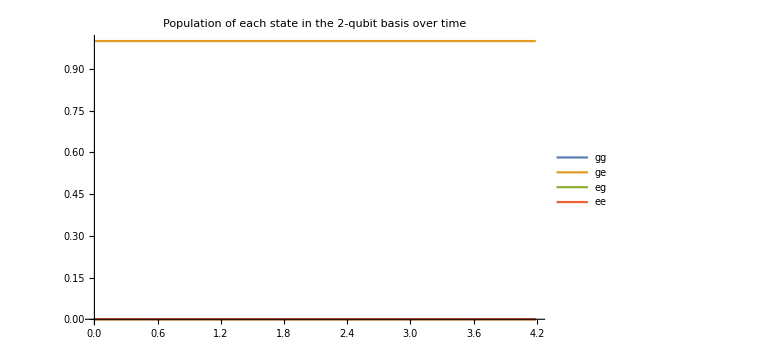
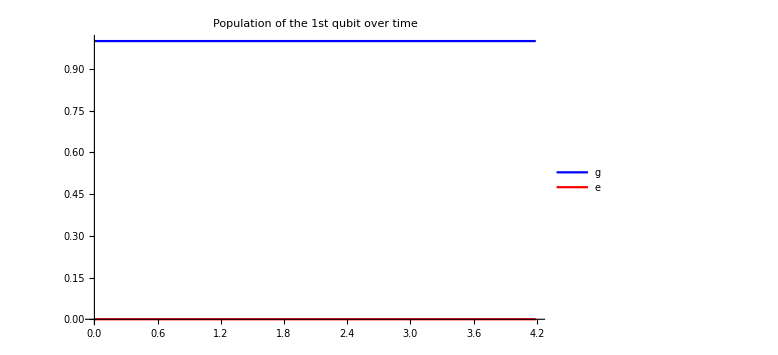
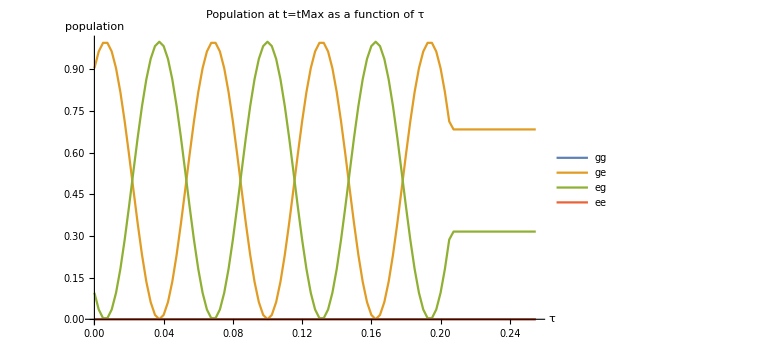
(-Graphics-
-Graphics-

-Graphics-)

```mathematica
out2=ListPlot[(Transpose[{Range[0,tMax,tRes],pops⟦All,#1,1⟧}]&)/@{1,2,3,4},PlotRange->All,PlotLabel->"Population of each state in the 2-qubit basis over time",PlotLegends->{"gg","ge","eg","ee"},ImageSize->Large,Joined->True];
out3=ListPlot[(Transpose[{Range[0,tMax,tRes],pops⟦All,#1,1⟧+pops⟦All,#1+1,1⟧}]&)/@{1,3},PlotRange->All,PlotLabel->"Population of the 1st qubit over time",PlotLegends->{"g","e"},ImageSize->Large,PlotStyle->{Blue,Red},Joined->True];
out4=Manipulate[{Show[Graphics3D[{{Blue,Thick,Arrow[{{0,0,0},{Px1[1+t/tRes],Py1[1+t/tRes],Pz1[1+t/tRes]}}]}},Boxed->False,PlotLabel->"Bloch spheres for qubits 1 and 2",ImageSize->Medium],ParametricPlot3D[{Px1[n],Py1[n],Pz1[n]},{n,1,tMax/tRes}],blochSphere],Show[Graphics3D[{{Red,Thick,Arrow[{{0,0,0},{Px2[1+t/tRes],Py2[1+t/tRes],Pz2[1+t/tRes]}}]}},Boxed->False],ParametricPlot3D[{Px2[n],Py2[n],Pz2[n]},{n,1,tMax/tRes},PlotStyle->Red],blochSphere,ImageSize->Medium]},{t,0,tMax-tRes,tRes}];
osc=ParallelTable[((N[Abs[#1]^2][[1]]&)/@(N[ReleaseHold[pulseSequence[9/10+16τ,τ]]].ψ0)),{τ,0,τ0,tRes/(4Length[pulseList])}]ᵀ;
osc=Thread[{Table[τ,{τ,0,τ0,tRes/(4Length[pulseList])}],#}]&/@osc;
out5=ListPlot[osc,PlotLabel->"Population at t=tMax as a function of τ",AxesLabel->{"τ","population"},PlotLegends->{"gg","ge","eg","ee"},ImageSize->Large,Joined->True];
({{out2}, {out3}, {out4}, {out5}})//MatrixForm
```

```mathematica
test
```

test

```mathematica
.
```